Задание 1.

1. Задаем начальные данные :

```mathematica
f[x_]:= 3^x;
```

```mathematica
n=7; a=-1;b=1;
```

```mathematica
Do[{Subscript[x, i]=Cos[(π(2*i+1))/(2*(n+1))],Subscript[f, i]=f[Subscript[x, i]]},{i,0,n}]
```

```mathematica
Unprotect[Power];0^0:=1;
```

2. Строим алгебраический интерполяционный многочлен:

```mathematica
Do[Subscript[l, k][x_]=(∏_(i=0)^(k-1) (x-Subscript[x, i])/(Subscript[x, k]-Subscript[x, i]))(∏_(i=k+1)^n (x-Subscript[x, i])/(Subscript[x, k]-Subscript[x, i])),{k,0,n}];
P[x_]=∑_(k=0)^n Subscript[l, k][x] Subscript[f, k] //Expand//N
```

1.+1.09861 x+0.603488 x^2+0.220996 x^3+0.0606295 x^4+0.0133283 x^5+0.00254916 x^6+0.000396293 x^7

3. Оценить погрешность интерполирования:

```mathematica
M=Maximize[{Abs[D[f[x],{x,n+1}]], a≤x≤b},x][[1]]//N
```

6.36615

```mathematica
M/((n+1)!*2^n)//N
```

1.23352×10^-6

4. Изображаем исходную систему точек и полученный интерполяционный многочлен в одной системе координат:

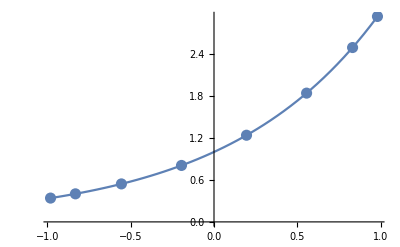

```mathematica
Gr1=ListPlot[Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}],PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x],{x,Subscript[x, 0],Subscript[x, n]}];
Show[Gr1,Gr2]
```

# Задание 2.

1. Задаем начальные данные :

```mathematica
f[x_]=Sin[9*x]; 
a=0;b=3;ϵ=10^-1;
```

2. Построить интерполяционный многочлен минимальной верхней гранью погрешности, не превышающей ϵ :

```mathematica
n=1;While[(1/((n+1)!*2^n)Maximize[{Abs[D[f[x],{x,n+1}]], a≤x≤b},x][[1]]*(b-a)^(n+1)//N) > ϵ,n++]; n
```

1

```mathematica
Do[{Subscript[x, i]=(b-a)/2*Cos[(π(2*i+1))/(2*(n+1))]+(a+b)/2,Subscript[f, i]=f[Subscript[x, i]]},{i,0,n}]
```

```mathematica
n = 12;
Do[Subscript[l, k][x_]=(∏_(i=0)^(k-1) (x-Subscript[x, i])/(Subscript[x, k]-Subscript[x, i]))(∏_(i=k+1)^n (x-Subscript[x, i])/(Subscript[x, k]-Subscript[x, i])),{k,0,n}];
P[x_]=∑_(k=0)^n Subscript[l, k][x] Subscript[f, k] //Expand//N
```

6648.64-174785. x+1.00027×10^6 x^2-2.65398×10^6 x^3+4.09408×10^6 x^4-4.06896×10^6 x^5+2.74422×10^6 x^6-1.28602×10^6 x^7+420019. x^8-93921.7 x^9+13721.4 x^10-1180.56 x^11+45.3733 x^12

3. Изображаем исходную систему точек и полученный интерполяционный многочлен в одной системе координат:

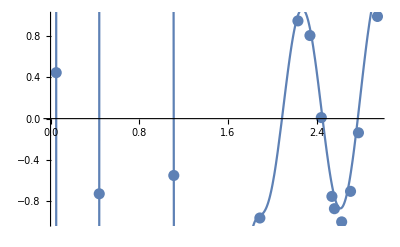

```mathematica
Gr1=ListPlot[Table[{Subscript[x, i],Subscript[f, i]},{i,0,n}],PlotStyle->{PointSize[0.02]}];
Gr2=Plot[P[x],{x,a,b}];
Show[Gr1,Gr2]
```

# Задание 3

1. Задаем начальные данные :

```mathematica
ff[x_]=E^x; 
Subscript[x, 0]=0;Subscript[x, 1]=0.1;Subscript[x, 2]=0.2;
```

2. Оценить погрешность приближения функции интерполяционным многочленом Лагранжа, построенным по узлам  в точке:

```mathematica
n=2;t1=0.05;t2=0.15;
ω[x_]=∏_(i=0)^n (x-Subscript[x, i])
```

(-0.2+x) (-0.1+x) x

```mathematica
M=Maximize[{Abs[D[ff[x],{x,n+1}]],0≤x≤0.2},x][[1]]//N
```

1.2214

```mathematica
R=M/((n+1)!)*Abs[ω[t1]]
```

0.0000763377

```mathematica
R=M/((n+1)!)*Abs[ω[t2]]
```

0.0000763377

# Задание 4

1. Задаем начальные данные :

```mathematica
fff[x_]=Cos[x]; 
a=0;
b=1;
```

2. Оценить погрешность интерполирования функции на отрезке:

```mathematica
n=5;
```

```mathematica
M=Maximize[{Abs[D[fff[x],{x,n+1}]],a≤x≤b},x][[1]]//N
```

1.

```mathematica
R=(M(b-a)^(n+1))/((n+1)!2^(2n+1))//N
```

6.78168×10^-7